Suppose that gmma = 3/2 H^2/R^2, and H = R, gmma is then 3/2.

```mathematica
A=1
gamma = 1.5
Jkrj=Table[u/.FindRoot[A×x^-3×ⅇ^(-J×x)×(ⅇ^-u+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-u×l))-1,{u,-0.0001}],{J,1,4,0.5},{x,0.1,20,0.1}]
```

1

1.5

{{6.82095,4.73973,3.66796,3.05675,2.67049,2.39946,2.19395,2.02961,1.89323,1.77701,1.67597,1.58678,1.50708,1.43517,1.36976,1.30986,1.25469,1.20363,1.15616,1.11187,1.0704,1.03147,0.994823,0.96024,0.927536,0.896548,0.867135,0.839172,0.812546,0.787158,0.762921,0.739755,0.717588,0.696355,0.675997,0.656462,0.637699,0.619665,0.602317,0.585619,0.569535,0.554033,0.539083,0.524658,0.510731,0.49728,0.48428,0.471712,0.459555,0.447792,0.436405,0.425378,0.414696,0.404344,0.394308,0.384577,0.375138,0.365979,0.35709,0.34846,0.34008,0.33194,0.324031,0.316346,0.308876,0.301613,0.294551,0.287682,0.281,0.274499,0.268171,0.262013,0.256017,0.25018,0.244495,0.238958,0.233565,0.22831,0.223189,0.218199,0.213335,0.208594,0.203971,0.199464,0.195069,0.190782,0.186601,0.182522,0.178542,0.174659,0.17087,0.167173,0.163564,0.160041,0.156602,0.153244,0.149966,0.146765,0.143639,0.140586,0.137604,0.134691,0.131846,0.129066,0.12635,0.123697,0.121104,0.11857,0.116093,0.113673,0.111307,0.108995,0.106734,0.104524,0.102364,0.100251,0.0981856,0.0961658,0.0941907,0.0922591,0.0903701,0.0885224,0.0867152,0.0849475,0.0832183,0.0815268,0.0798719,0.0782528,0.0766687,0.0751188,0.0736022,0.0721181,0.0706659,0.0692447,0.0678539,0.0664927,0.0651604,0.0638564,0.06258,0.0613306,0.0601075,0.0589103,0.0577382,0.0565907,0.0554673,0.0543674,0.0532905,0.052236,0.0512035,0.0501924,0.0492024,0.0482328,0.0472834,0.0463535,0.0454428,0.0445509,0.0436774,0.0428217,0.0419837,0.0411628,0.0403587,0.039571,0.0387994,0.0380435,0.037303,0.0365776,0.0358668,0.0351705,0.0344883,0.0338198,0.0331649,0.0325232,0.0318944,0.0312782,0.0306745,0.0300829,0.0295031,0.0289349,0.0283781,0.0278325,0.0272977,0.0267736,0.0262599,0.0257565,0.025263,0.0247794,0.0243053,0.0238407,0.0233852,0.0229388,0.0225012,0.0220722,0.0216517,0.0212394,0.0208353,0.0204391,0.0200508,0.01967,0.0192967,0.0189307},{6.77162,4.65073,3.56246,2.94854,2.56074,2.28681,2.07742,1.90873,1.76788,1.64726,1.542,1.44884,1.36546,1.29015,1.22164,1.15892,1.10122,1.04789,0.998406,0.952347,0.909344,0.869091,0.831323,0.795812,0.76236,0.730794,0.70096,0.672723,0.645963,0.620571,0.596451,0.573515,0.551684,0.530886,0.511055,0.492133,0.474064,0.456797,0.440287,0.424491,0.409368,0.394884,0.381003,0.367693,0.354926,0.342675,0.330912,0.319615,0.30876,0.298327,0.288296,0.278648,0.269366,0.260433,0.251833,0.243552,0.235575,0.22789,0.220485,0.213346,0.206464,0.199827,0.193425,0.187249,0.18129,0.175538,0.169986,0.164626,0.15945,0.154451,0.149622,0.144957,0.14045,0.136093,0.131883,0.127813,0.123879,0.120074,0.116395,0.112837,0.109395,0.106065,0.102844,0.0997267,0.0967104,0.0937911,0.0909655,0.0882304,0.0855824,0.0830188,0.0805364,0.0781326,0.0758046,0.0735498,0.0713658,0.0692502,0.0672006,0.0652149,0.0632909,0.0614265,0.0596198,0.0578689,0.0561718,0.054527,0.0529325,0.0513868,0.0498884,0.0484356,0.0470269,0.0456611,0.0443366,0.0430521,0.0418065,0.0405983,0.0394265,0.0382899,0.0371873,0.0361177,0.0350801,0.0340734,0.0330967,0.032149,0.0312295,0.0303371,0.0294712,0.0286309,0.0278154,0.0270239,0.0262556,0.02551,0.0247862,0.0240836,0.0234016,0.0227395,0.0220967,0.0214726,0.0208667,0.0202785,0.0197073,0.0191526,0.0186141,0.0180911,0.0175832,0.01709,0.016611,0.0161458,0.015694,0.0152551,0.0148289,0.0144149,0.0140127,0.0136221,0.0132426,0.0128739,0.0125158,0.0121679,0.0118299,0.0115015,0.0111824,0.0108724,0.0105712,0.0102785,0.00999414,0.0097178,0.00944927,0.00918833,0.00893475,0.00868832,0.00844883,0.00821608,0.00798988,0.00777004,0.00755637,0.0073487,0.00714684,0.00695065,0.00675995,0.00657458,0.00639439,0.00621924,0.00604897,0.00588346,0.00572256,0.00556614,0.00541407,0.00526624,0.00512251,0.00498278,0.00484692,0.00471484,0.00458641,0.00446155,0.00434014,0.00422209,0.0041073,0.00399569,0.00388716,0.00378163,0.00367901,0.00357921},{6.72233,4.56272,3.46081,2.84606,2.45744,2.18106,1.96828,1.79586,1.65127,1.52711,1.4186,1.32251,1.23656,1.15903,1.08864,1.02437,0.96541,0.911114,0.860936,0.814424,0.771197,0.730928,0.693335,0.658176,0.625235,0.594327,0.565284,0.537959,0.51222,0.487948,0.465038,0.443391,0.422922,0.40355,0.385202,0.367813,0.351322,0.335671,0.320811,0.306693,0.293272,0.28051,0.268366,0.256807,0.2458,0.235314,0.22532,0.215793,0.206707,0.198039,0.189767,0.18187,0.174331,0.167129,0.160249,0.153674,0.14739,0.141381,0.135635,0.13014,0.124882,0.11985,0.115035,0.110426,0.106012,0.101786,0.0977387,0.0938613,0.0901466,0.086587,0.0831756,0.0799058,0.0767712,0.0737659,0.0708841,0.0681204,0.0654695,0.0629267,0.0604872,0.0581466,0.0559005,0.053745,0.0516761,0.0496902,0.0477837,0.0459533,0.0441958,0.0425082,0.0408874,0.0393307,0.0378355,0.0363992,0.0350193,0.0336936,0.0324198,0.0311958,0.0300195,0.028889,0.0278024,0.026758,0.0257541,0.024789,0.0238611,0.022969,0.0221112,0.0212864,0.0204932,0.0197303,0.0189967,0.0182911,0.0176123,0.0169595,0.0163314,0.0157272,0.0151459,0.0145866,0.0140485,0.0135307,0.0130325,0.012553,0.0120915,0.0116474,0.01122,0.0108086,0.0104127,0.0100315,0.00966459,0.00931138,0.00897135,0.00864398,0.0083288,0.00802534,0.00773315,0.00745181,0.0071809,0.00692002,0.00666879,0.00642685,0.00619385,0.00596945,0.00575332,0.00554515,0.00534465,0.00515151,0.00496548,0.00478627,0.00461364,0.00444733,0.00428712,0.00413277,0.00398406,0.00384079,0.00370275,0.00356974,0.00344158,0.0033181,0.0031991,0.00308444,0.00297395,0.00286747,0.00276485,0.00266596,0.00257065,0.0024788,0.00239027,0.00230495,0.00222271,0.00214344,0.00206703,0.00199338,0.00192237,0.00185392,0.00178791,0.00172427,0.00166289,0.00160368,0.00154655,0.00149141,0.00143817,0.00138674,0.00133704,0.00128898,0.00124247,0.00119743,0.00115378,0.00111143,0.00107032,0.00103035,0.000991475,0.000953609,0.000916692,0.000880661,0.000845457,0.000811025,0.000777313,0.000744273,0.000711858,0.000680027,0.00064874,0.00061796},{6.67307,4.47577,3.363,2.74892,2.35994,2.08143,1.86568,1.69009,1.54247,1.41557,1.3047,1.20666,1.11914,1.04045,0.969244,0.904501,0.845379,0.791195,0.741381,0.695459,0.653024,0.613726,0.577264,0.543375,0.51183,0.482423,0.454976,0.429326,0.405332,0.382863,0.361802,0.342046,0.323497,0.30607,0.289686,0.274271,0.25976,0.246091,0.23321,0.221064,0.209605,0.198791,0.18858,0.178935,0.169821,0.161205,0.153057,0.14535,0.138057,0.131153,0.124617,0.118426,0.112561,0.107003,0.101735,0.0967408,0.0920046,0.0875123,0.0832505,0.0792063,0.0753681,0.0717245,0.0682651,0.06498,0.0618598,0.0588958,0.0560797,0.0534036,0.0508604,0.0484429,0.0461446,0.0439594,0.0418815,0.0399052,0.0380254,0.0362372,0.0345358,0.0329169,0.0313763,0.0299101,0.0285145,0.0271859,0.0259211,0.0247168,0.02357,0.0224779,0.0214378,0.0204471,0.0195034,0.0186043,0.0177478,0.0169316,0.0161539,0.0154128,0.0147065,0.0140333,0.0133916,0.0127799,0.0121967,0.0116408,0.0111107,0.0106052,0.0101232,0.00966361,0.00922526,0.00880718,0.00840841,0.00802803,0.00766519,0.00731904,0.0069888,0.00667373,0.00637311,0.00608627,0.00581255,0.00555135,0.00530208,0.00506419,0.00483714,0.00462042,0.00441357,0.00421612,0.00402764,0.0038477,0.00367593,0.00351193,0.00335535,0.00320585,0.00306311,0.00292681,0.00279665,0.00267236,0.00255366,0.00244031,0.00233205,0.00222865,0.00212989,0.00203556,0.00194544,0.00185935,0.00177709,0.00169848,0.00162333,0.00155147,0.00148273,0.00141692,0.00135388,0.00129344,0.00123543,0.00117969,0.00112606,0.00107439,0.00102453,0.000976338,0.000929687,0.00088445,0.000840512,0.000797765,0.000756111,0.000715456,0.000675718,0.000636821,0.000598693,0.000561271,0.000524497,0.000488318,0.000452687,0.000417559,0.000382895,0.00034866,0.00031482,0.000281345,0.00024821,0.000215388,0.000182859,0.0001506,0.000118595,0.0000868249,0.0000552752,0.0000239312,-7.21988×10^-6,-0.0000381902,-0.0000689907,-0.0000996315,-0.000130122,-0.000160471,-0.000190685,-0.000220774,-0.000250742,-0.000280597,-0.000310345,-0.00033999,-0.000369538,-0.000398994,-0.000428361,-0.000457645,-0.000486848,-0.000515974,-0.000545027,-0.00057401},{6.62385,4.38996,3.269,2.6567,2.26764,1.98725,1.76894,1.59072,1.44074,1.31186,1.19947,1.10036,1.0122,0.933259,0.862173,0.797868,0.739471,0.686262,0.637642,0.593102,0.55221,0.514593,0.479927,0.44793,0.418354,0.390979,0.365612,0.342079,0.320226,0.299913,0.281017,0.263423,0.24703,0.231745,0.217485,0.204171,0.191735,0.180112,0.169243,0.159074,0.149556,0.140644,0.132295,0.124471,0.117136,0.110256,0.103803,0.0977463,0.0920609,0.0867222,0.0817076,0.0769962,0.0725685,0.0684063,0.0644928,0.0608123,0.0573501,0.0540926,0.0510271,0.0481416,0.0454251,0.0428672,0.0404581,0.0381889,0.0360511,0.0340367,0.0321382,0.0303489,0.028662,0.0270716,0.0255719,0.0241575,0.0228234,0.0215649,0.0203776,0.0192573,0.0182,0.0172022,0.0162604,0.0153713,0.0145319,0.0137394,0.012991,0.0122842,0.0116167,0.0109861,0.0103905,0.00982781,0.00929617,0.00879382,0.00831912,0.0078705,0.0074465,0.00704574,0.00666692,0.0063088,0.00597024,0.00565014,0.00534747,0.00506127,0.00479063,0.00453467,0.00429259,0.00406362,0.00384704,0.00364216,0.00344835,0.00326499,0.00309151,0.00292737,0.00277206,0.00262509,0.00248601,0.00235439,0.00222983,0.00211192,0.00200032,0.00189467,0.00179464,0.0016999,0.00161014,0.00152507,0.00144436,0.00136774,0.00129491,0.00122557,0.00115946,0.00109629,0.00103582,0.000977791,0.00092198,0.000868174,0.000816175,0.000765807,0.000716907,0.000669328,0.000622939,0.000577623,0.000533273,0.000489797,0.000447109,0.000405137,0.000363812,0.000323076,0.000282875,0.000243163,0.000203897,0.00016504,0.000126558,0.0000884202,0.0000505997,0.0000130721,-0.0000241846,-0.0000611905,-0.0000979634,-0.00013452,-0.000170874,-0.00020704,-0.000243029,-0.000278854,-0.000314523,-0.000350047,-0.000385433,-0.00042069,-0.000455825,-0.000490844,-0.000525754,-0.00056056,-0.000595268,-0.000629881,-0.000664406,-0.000698845,-0.000733203,-0.000767484,-0.00080169,-0.000835825,-0.000869892,-0.000903894,-0.000937832,-0.000971711,-0.00100553,-0.0010393,-0.00107301,-0.00110667,-0.00114027,-0.00117383,-0.00120735,-0.00124081,-0.00127424,-0.00130762,-0.00134096,-0.00137426,-0.00140752,-0.00144075,-0.00147394,-0.00150709,-0.00154021,-0.00157329,-0.00160634,-0.00163936},{6.57467,4.30536,3.17874,2.56903,2.18003,1.89798,1.67748,1.49718,1.34548,1.21537,1.10223,1.00285,0.914857,0.836469,0.766276,0.703157,0.646194,0.594628,0.547824,0.505241,0.466419,0.43096,0.398519,0.368794,0.341522,0.316468,0.293426,0.272213,0.252664,0.234633,0.217988,0.202612,0.188396,0.175246,0.163072,0.151797,0.141348,0.131659,0.122671,0.114329,0.106583,0.0993879,0.0927014,0.0864854,0.0807047,0.0753268,0.0703222,0.0656634,0.0613251,0.0572843,0.0535195,0.0500108,0.04674,0.0436903,0.040846,0.0381927,0.035717,0.0334066,0.0312499,0.0292364,0.0273562,0.0256001,0.0239597,0.0224271,0.0209949,0.0196564,0.0184052,0.0172355,0.0161418,0.015119,0.0141624,0.0132676,0.0124304,0.0116472,0.0109142,0.0102283,0.00958627,0.00898527,0.00842262,0.00789582,0.00740253,0.00694058,0.00650792,0.00610266,0.00572304,0.00536739,0.00503418,0.00472196,0.00442938,0.00415519,0.00389821,0.00365734,0.00343155,0.00321988,0.00302144,0.00283538,0.00266093,0.00249733,0.00234392,0.00220003,0.00206508,0.00193848,0.00181971,0.00170823,0.00160356,0.00150522,0.00141272,0.0013256,0.00124341,0.00116568,0.001092,0.00102195,0.000955153,0.000891248,0.000829912,0.000770854,0.000713812,0.000658555,0.000604876,0.000552596,0.000501557,0.00045162,0.000402665,0.000354585,0.000307288,0.000260693,0.000214729,0.000169334,0.000124453,0.0000800377,0.0000360462,-7.55946×10^-6,-0.0000508125,-0.0000937425,-0.000136376,-0.000178736,-0.000220843,-0.000262718,-0.000304375,-0.000345831,-0.0003871,-0.000428194,-0.000469123,-0.000509899,-0.000550531,-0.000591027,-0.000631394,-0.000671641,-0.000711774,-0.000751798,-0.000791719,-0.000831543,-0.000871273,-0.000910915,-0.000950473,-0.00098995,-0.00102935,-0.00106868,-0.00110793,-0.00114712,-0.00118624,-0.0012253,-0.0012643,-0.00130324,-0.00134212,-0.00138095,-0.00141973,-0.00145846,-0.00149714,-0.00153577,-0.00157436,-0.0016129,-0.0016514,-0.00168986,-0.00172828,-0.00176666,-0.001805,-0.0018433,-0.00188157,-0.0019198,-0.00195799,-0.00199616,-0.00203429,-0.00207239,-0.00211046,-0.0021485,-0.00218651,-0.00222449,-0.00226244,-0.00230037,-0.00233827,-0.00237614,-0.00241399,-0.00245181,-0.00248961,-0.00252738,-0.00256513,-0.00260286,-0.00264056,-0.00267824},{6.52553,4.22203,3.09211,2.48552,2.09665,1.81315,1.59087,1.40901,1.25622,1.12555,1.01238,0.913449,0.826329,0.74917,0.680509,0.61917,0.564187,0.51476,0.470215,0.429981,0.39357,0.36056,0.330587,0.303332,0.278516,0.255895,0.235253,0.216396,0.199155,0.183378,0.168928,0.155686,0.14354,0.132394,0.122158,0.112753,0.104107,0.0961546,0.0888365,0.0820991,0.0758936,0.0701757,0.0649051,0.0600448,0.0555615,0.0514243,0.0476055,0.0440794,0.0408225,0.0378136,0.0350328,0.0324624,0.0300857,0.0278877,0.0258544,0.0239731,0.0222319,0.0206203,0.0191282,0.0177464,0.0164667,0.0152812,0.0141828,0.0131649,0.0122215,0.011347,0.0105363,0.00978451,0.00908733,0.00844068,0.00784083,0.0072843,0.00676791,0.00628871,0.00584395,0.00543112,0.00504788,0.00469207,0.00436169,0.00405489,0.00376996,0.00350532,0.00325949,0.00303111,0.00281894,0.00262179,0.0024386,0.00226835,0.00211012,0.00196303,0.00182627,0.00169908,0.0015807,0.00147043,0.00136756,0.00127139,0.00118126,0.00109652,0.00101654,0.00094077,0.000868672,0.000799784,0.000733691,0.000670027,0.000608476,0.000548766,0.00049066,0.000433956,0.00037848,0.000324085,0.000270641,0.000218039,0.000166184,0.000114996,0.0000644024,0.0000143435,-0.0000352344,-0.0000843776,-0.000133127,-0.000181517,-0.000229581,-0.000277344,-0.000324833,-0.000372068,-0.000419069,-0.000465854,-0.000512437,-0.000558832,-0.000605053,-0.000651111,-0.000697015,-0.000742775,-0.000788399,-0.000833896,-0.000879272,-0.000924534,-0.000969688,-0.00101474,-0.00105969,-0.00110455,-0.00114932,-0.00119401,-0.00123861,-0.00128314,-0.0013276,-0.00137198,-0.00141629,-0.00146054,-0.00150472,-0.00154885,-0.00159291,-0.00163692,-0.00168087,-0.00172477,-0.00176862,-0.00181242,-0.00185617,-0.00189988,-0.00194354,-0.00198715,-0.00203073,-0.00207426,-0.00211775,-0.00216121,-0.00220462,-0.002248,-0.00229134,-0.00233465,-0.00237792,-0.00242116,-0.00246437,-0.00250755,-0.00255069,-0.00259381,-0.00263689,-0.00267995,-0.00272297,-0.00276597,-0.00280895,-0.00285189,-0.00289481,-0.00293771,-0.00298058,-0.00302342,-0.00306624,-0.00310904,-0.00315182,-0.00319457,-0.0032373,-0.00328001,-0.0033227,-0.00336536,-0.00340801,-0.00345063,-0.00349324,-0.00353583,-0.00357839,-0.00362094,-0.00366347,-0.00370598}}

```mathematica
J1 = Jkrj[[1]]
J105 = Jkrj[[2]]
J2 = Jkrj[[3]]
J205=Jkrj[[4]]
J3 = Jkrj[[5]]
J305= Jkrj[[6]]
J4 = Jkrj[[7]]
```

{6.82095,4.73973,3.66796,3.05675,2.67049,2.39946,2.19395,2.02961,1.89323,1.77701,1.67597,1.58678,1.50708,1.43517,1.36976,1.30986,1.25469,1.20363,1.15616,1.11187,1.0704,1.03147,0.994823,0.96024,0.927536,0.896548,0.867135,0.839172,0.812546,0.787158,0.762921,0.739755,0.717588,0.696355,0.675997,0.656462,0.637699,0.619665,0.602317,0.585619,0.569535,0.554033,0.539083,0.524658,0.510731,0.49728,0.48428,0.471712,0.459555,0.447792,0.436405,0.425378,0.414696,0.404344,0.394308,0.384577,0.375138,0.365979,0.35709,0.34846,0.34008,0.33194,0.324031,0.316346,0.308876,0.301613,0.294551,0.287682,0.281,0.274499,0.268171,0.262013,0.256017,0.25018,0.244495,0.238958,0.233565,0.22831,0.223189,0.218199,0.213335,0.208594,0.203971,0.199464,0.195069,0.190782,0.186601,0.182522,0.178542,0.174659,0.17087,0.167173,0.163564,0.160041,0.156602,0.153244,0.149966,0.146765,0.143639,0.140586,0.137604,0.134691,0.131846,0.129066,0.12635,0.123697,0.121104,0.11857,0.116093,0.113673,0.111307,0.108995,0.106734,0.104524,0.102364,0.100251,0.0981856,0.0961658,0.0941907,0.0922591,0.0903701,0.0885224,0.0867152,0.0849475,0.0832183,0.0815268,0.0798719,0.0782528,0.0766687,0.0751188,0.0736022,0.0721181,0.0706659,0.0692447,0.0678539,0.0664927,0.0651604,0.0638564,0.06258,0.0613306,0.0601075,0.0589103,0.0577382,0.0565907,0.0554673,0.0543674,0.0532905,0.052236,0.0512035,0.0501924,0.0492024,0.0482328,0.0472834,0.0463535,0.0454428,0.0445509,0.0436774,0.0428217,0.0419837,0.0411628,0.0403587,0.039571,0.0387994,0.0380435,0.037303,0.0365776,0.0358668,0.0351705,0.0344883,0.0338198,0.0331649,0.0325232,0.0318944,0.0312782,0.0306745,0.0300829,0.0295031,0.0289349,0.0283781,0.0278325,0.0272977,0.0267736,0.0262599,0.0257565,0.025263,0.0247794,0.0243053,0.0238407,0.0233852,0.0229388,0.0225012,0.0220722,0.0216517,0.0212394,0.0208353,0.0204391,0.0200508,0.01967,0.0192967,0.0189307}

{6.77162,4.65073,3.56246,2.94854,2.56074,2.28681,2.07742,1.90873,1.76788,1.64726,1.542,1.44884,1.36546,1.29015,1.22164,1.15892,1.10122,1.04789,0.998406,0.952347,0.909344,0.869091,0.831323,0.795812,0.76236,0.730794,0.70096,0.672723,0.645963,0.620571,0.596451,0.573515,0.551684,0.530886,0.511055,0.492133,0.474064,0.456797,0.440287,0.424491,0.409368,0.394884,0.381003,0.367693,0.354926,0.342675,0.330912,0.319615,0.30876,0.298327,0.288296,0.278648,0.269366,0.260433,0.251833,0.243552,0.235575,0.22789,0.220485,0.213346,0.206464,0.199827,0.193425,0.187249,0.18129,0.175538,0.169986,0.164626,0.15945,0.154451,0.149622,0.144957,0.14045,0.136093,0.131883,0.127813,0.123879,0.120074,0.116395,0.112837,0.109395,0.106065,0.102844,0.0997267,0.0967104,0.0937911,0.0909655,0.0882304,0.0855824,0.0830188,0.0805364,0.0781326,0.0758046,0.0735498,0.0713658,0.0692502,0.0672006,0.0652149,0.0632909,0.0614265,0.0596198,0.0578689,0.0561718,0.054527,0.0529325,0.0513868,0.0498884,0.0484356,0.0470269,0.0456611,0.0443366,0.0430521,0.0418065,0.0405983,0.0394265,0.0382899,0.0371873,0.0361177,0.0350801,0.0340734,0.0330967,0.032149,0.0312295,0.0303371,0.0294712,0.0286309,0.0278154,0.0270239,0.0262556,0.02551,0.0247862,0.0240836,0.0234016,0.0227395,0.0220967,0.0214726,0.0208667,0.0202785,0.0197073,0.0191526,0.0186141,0.0180911,0.0175832,0.01709,0.016611,0.0161458,0.015694,0.0152551,0.0148289,0.0144149,0.0140127,0.0136221,0.0132426,0.0128739,0.0125158,0.0121679,0.0118299,0.0115015,0.0111824,0.0108724,0.0105712,0.0102785,0.00999414,0.0097178,0.00944927,0.00918833,0.00893475,0.00868832,0.00844883,0.00821608,0.00798988,0.00777004,0.00755637,0.0073487,0.00714684,0.00695065,0.00675995,0.00657458,0.00639439,0.00621924,0.00604897,0.00588346,0.00572256,0.00556614,0.00541407,0.00526624,0.00512251,0.00498278,0.00484692,0.00471484,0.00458641,0.00446155,0.00434014,0.00422209,0.0041073,0.00399569,0.00388716,0.00378163,0.00367901,0.00357921}

{6.72233,4.56272,3.46081,2.84606,2.45744,2.18106,1.96828,1.79586,1.65127,1.52711,1.4186,1.32251,1.23656,1.15903,1.08864,1.02437,0.96541,0.911114,0.860936,0.814424,0.771197,0.730928,0.693335,0.658176,0.625235,0.594327,0.565284,0.537959,0.51222,0.487948,0.465038,0.443391,0.422922,0.40355,0.385202,0.367813,0.351322,0.335671,0.320811,0.306693,0.293272,0.28051,0.268366,0.256807,0.2458,0.235314,0.22532,0.215793,0.206707,0.198039,0.189767,0.18187,0.174331,0.167129,0.160249,0.153674,0.14739,0.141381,0.135635,0.13014,0.124882,0.11985,0.115035,0.110426,0.106012,0.101786,0.0977387,0.0938613,0.0901466,0.086587,0.0831756,0.0799058,0.0767712,0.0737659,0.0708841,0.0681204,0.0654695,0.0629267,0.0604872,0.0581466,0.0559005,0.053745,0.0516761,0.0496902,0.0477837,0.0459533,0.0441958,0.0425082,0.0408874,0.0393307,0.0378355,0.0363992,0.0350193,0.0336936,0.0324198,0.0311958,0.0300195,0.028889,0.0278024,0.026758,0.0257541,0.024789,0.0238611,0.022969,0.0221112,0.0212864,0.0204932,0.0197303,0.0189967,0.0182911,0.0176123,0.0169595,0.0163314,0.0157272,0.0151459,0.0145866,0.0140485,0.0135307,0.0130325,0.012553,0.0120915,0.0116474,0.01122,0.0108086,0.0104127,0.0100315,0.00966459,0.00931138,0.00897135,0.00864398,0.0083288,0.00802534,0.00773315,0.00745181,0.0071809,0.00692002,0.00666879,0.00642685,0.00619385,0.00596945,0.00575332,0.00554515,0.00534465,0.00515151,0.00496548,0.00478627,0.00461364,0.00444733,0.00428712,0.00413277,0.00398406,0.00384079,0.00370275,0.00356974,0.00344158,0.0033181,0.0031991,0.00308444,0.00297395,0.00286747,0.00276485,0.00266596,0.00257065,0.0024788,0.00239027,0.00230495,0.00222271,0.00214344,0.00206703,0.00199338,0.00192237,0.00185392,0.00178791,0.00172427,0.00166289,0.00160368,0.00154655,0.00149141,0.00143817,0.00138674,0.00133704,0.00128898,0.00124247,0.00119743,0.00115378,0.00111143,0.00107032,0.00103035,0.000991475,0.000953609,0.000916692,0.000880661,0.000845457,0.000811025,0.000777313,0.000744273,0.000711858,0.000680027,0.00064874,0.00061796}

{6.67307,4.47577,3.363,2.74892,2.35994,2.08143,1.86568,1.69009,1.54247,1.41557,1.3047,1.20666,1.11914,1.04045,0.969244,0.904501,0.845379,0.791195,0.741381,0.695459,0.653024,0.613726,0.577264,0.543375,0.51183,0.482423,0.454976,0.429326,0.405332,0.382863,0.361802,0.342046,0.323497,0.30607,0.289686,0.274271,0.25976,0.246091,0.23321,0.221064,0.209605,0.198791,0.18858,0.178935,0.169821,0.161205,0.153057,0.14535,0.138057,0.131153,0.124617,0.118426,0.112561,0.107003,0.101735,0.0967408,0.0920046,0.0875123,0.0832505,0.0792063,0.0753681,0.0717245,0.0682651,0.06498,0.0618598,0.0588958,0.0560797,0.0534036,0.0508604,0.0484429,0.0461446,0.0439594,0.0418815,0.0399052,0.0380254,0.0362372,0.0345358,0.0329169,0.0313763,0.0299101,0.0285145,0.0271859,0.0259211,0.0247168,0.02357,0.0224779,0.0214378,0.0204471,0.0195034,0.0186043,0.0177478,0.0169316,0.0161539,0.0154128,0.0147065,0.0140333,0.0133916,0.0127799,0.0121967,0.0116408,0.0111107,0.0106052,0.0101232,0.00966361,0.00922526,0.00880718,0.00840841,0.00802803,0.00766519,0.00731904,0.0069888,0.00667373,0.00637311,0.00608627,0.00581255,0.00555135,0.00530208,0.00506419,0.00483714,0.00462042,0.00441357,0.00421612,0.00402764,0.0038477,0.00367593,0.00351193,0.00335535,0.00320585,0.00306311,0.00292681,0.00279665,0.00267236,0.00255366,0.00244031,0.00233205,0.00222865,0.00212989,0.00203556,0.00194544,0.00185935,0.00177709,0.00169848,0.00162333,0.00155147,0.00148273,0.00141692,0.00135388,0.00129344,0.00123543,0.00117969,0.00112606,0.00107439,0.00102453,0.000976338,0.000929687,0.00088445,0.000840512,0.000797765,0.000756111,0.000715456,0.000675718,0.000636821,0.000598693,0.000561271,0.000524497,0.000488318,0.000452687,0.000417559,0.000382895,0.00034866,0.00031482,0.000281345,0.00024821,0.000215388,0.000182859,0.0001506,0.000118595,0.0000868249,0.0000552752,0.0000239312,-7.21988×10^-6,-0.0000381902,-0.0000689907,-0.0000996315,-0.000130122,-0.000160471,-0.000190685,-0.000220774,-0.000250742,-0.000280597,-0.000310345,-0.00033999,-0.000369538,-0.000398994,-0.000428361,-0.000457645,-0.000486848,-0.000515974,-0.000545027,-0.00057401}

{6.62385,4.38996,3.269,2.6567,2.26764,1.98725,1.76894,1.59072,1.44074,1.31186,1.19947,1.10036,1.0122,0.933259,0.862173,0.797868,0.739471,0.686262,0.637642,0.593102,0.55221,0.514593,0.479927,0.44793,0.418354,0.390979,0.365612,0.342079,0.320226,0.299913,0.281017,0.263423,0.24703,0.231745,0.217485,0.204171,0.191735,0.180112,0.169243,0.159074,0.149556,0.140644,0.132295,0.124471,0.117136,0.110256,0.103803,0.0977463,0.0920609,0.0867222,0.0817076,0.0769962,0.0725685,0.0684063,0.0644928,0.0608123,0.0573501,0.0540926,0.0510271,0.0481416,0.0454251,0.0428672,0.0404581,0.0381889,0.0360511,0.0340367,0.0321382,0.0303489,0.028662,0.0270716,0.0255719,0.0241575,0.0228234,0.0215649,0.0203776,0.0192573,0.0182,0.0172022,0.0162604,0.0153713,0.0145319,0.0137394,0.012991,0.0122842,0.0116167,0.0109861,0.0103905,0.00982781,0.00929617,0.00879382,0.00831912,0.0078705,0.0074465,0.00704574,0.00666692,0.0063088,0.00597024,0.00565014,0.00534747,0.00506127,0.00479063,0.00453467,0.00429259,0.00406362,0.00384704,0.00364216,0.00344835,0.00326499,0.00309151,0.00292737,0.00277206,0.00262509,0.00248601,0.00235439,0.00222983,0.00211192,0.00200032,0.00189467,0.00179464,0.0016999,0.00161014,0.00152507,0.00144436,0.00136774,0.00129491,0.00122557,0.00115946,0.00109629,0.00103582,0.000977791,0.00092198,0.000868174,0.000816175,0.000765807,0.000716907,0.000669328,0.000622939,0.000577623,0.000533273,0.000489797,0.000447109,0.000405137,0.000363812,0.000323076,0.000282875,0.000243163,0.000203897,0.00016504,0.000126558,0.0000884202,0.0000505997,0.0000130721,-0.0000241846,-0.0000611905,-0.0000979634,-0.00013452,-0.000170874,-0.00020704,-0.000243029,-0.000278854,-0.000314523,-0.000350047,-0.000385433,-0.00042069,-0.000455825,-0.000490844,-0.000525754,-0.00056056,-0.000595268,-0.000629881,-0.000664406,-0.000698845,-0.000733203,-0.000767484,-0.00080169,-0.000835825,-0.000869892,-0.000903894,-0.000937832,-0.000971711,-0.00100553,-0.0010393,-0.00107301,-0.00110667,-0.00114027,-0.00117383,-0.00120735,-0.00124081,-0.00127424,-0.00130762,-0.00134096,-0.00137426,-0.00140752,-0.00144075,-0.00147394,-0.00150709,-0.00154021,-0.00157329,-0.00160634,-0.00163936}

{6.57467,4.30536,3.17874,2.56903,2.18003,1.89798,1.67748,1.49718,1.34548,1.21537,1.10223,1.00285,0.914857,0.836469,0.766276,0.703157,0.646194,0.594628,0.547824,0.505241,0.466419,0.43096,0.398519,0.368794,0.341522,0.316468,0.293426,0.272213,0.252664,0.234633,0.217988,0.202612,0.188396,0.175246,0.163072,0.151797,0.141348,0.131659,0.122671,0.114329,0.106583,0.0993879,0.0927014,0.0864854,0.0807047,0.0753268,0.0703222,0.0656634,0.0613251,0.0572843,0.0535195,0.0500108,0.04674,0.0436903,0.040846,0.0381927,0.035717,0.0334066,0.0312499,0.0292364,0.0273562,0.0256001,0.0239597,0.0224271,0.0209949,0.0196564,0.0184052,0.0172355,0.0161418,0.015119,0.0141624,0.0132676,0.0124304,0.0116472,0.0109142,0.0102283,0.00958627,0.00898527,0.00842262,0.00789582,0.00740253,0.00694058,0.00650792,0.00610266,0.00572304,0.00536739,0.00503418,0.00472196,0.00442938,0.00415519,0.00389821,0.00365734,0.00343155,0.00321988,0.00302144,0.00283538,0.00266093,0.00249733,0.00234392,0.00220003,0.00206508,0.00193848,0.00181971,0.00170823,0.00160356,0.00150522,0.00141272,0.0013256,0.00124341,0.00116568,0.001092,0.00102195,0.000955153,0.000891248,0.000829912,0.000770854,0.000713812,0.000658555,0.000604876,0.000552596,0.000501557,0.00045162,0.000402665,0.000354585,0.000307288,0.000260693,0.000214729,0.000169334,0.000124453,0.0000800377,0.0000360462,-7.55946×10^-6,-0.0000508125,-0.0000937425,-0.000136376,-0.000178736,-0.000220843,-0.000262718,-0.000304375,-0.000345831,-0.0003871,-0.000428194,-0.000469123,-0.000509899,-0.000550531,-0.000591027,-0.000631394,-0.000671641,-0.000711774,-0.000751798,-0.000791719,-0.000831543,-0.000871273,-0.000910915,-0.000950473,-0.00098995,-0.00102935,-0.00106868,-0.00110793,-0.00114712,-0.00118624,-0.0012253,-0.0012643,-0.00130324,-0.00134212,-0.00138095,-0.00141973,-0.00145846,-0.00149714,-0.00153577,-0.00157436,-0.0016129,-0.0016514,-0.00168986,-0.00172828,-0.00176666,-0.001805,-0.0018433,-0.00188157,-0.0019198,-0.00195799,-0.00199616,-0.00203429,-0.00207239,-0.00211046,-0.0021485,-0.00218651,-0.00222449,-0.00226244,-0.00230037,-0.00233827,-0.00237614,-0.00241399,-0.00245181,-0.00248961,-0.00252738,-0.00256513,-0.00260286,-0.00264056,-0.00267824}

{6.52553,4.22203,3.09211,2.48552,2.09665,1.81315,1.59087,1.40901,1.25622,1.12555,1.01238,0.913449,0.826329,0.74917,0.680509,0.61917,0.564187,0.51476,0.470215,0.429981,0.39357,0.36056,0.330587,0.303332,0.278516,0.255895,0.235253,0.216396,0.199155,0.183378,0.168928,0.155686,0.14354,0.132394,0.122158,0.112753,0.104107,0.0961546,0.0888365,0.0820991,0.0758936,0.0701757,0.0649051,0.0600448,0.0555615,0.0514243,0.0476055,0.0440794,0.0408225,0.0378136,0.0350328,0.0324624,0.0300857,0.0278877,0.0258544,0.0239731,0.0222319,0.0206203,0.0191282,0.0177464,0.0164667,0.0152812,0.0141828,0.0131649,0.0122215,0.011347,0.0105363,0.00978451,0.00908733,0.00844068,0.00784083,0.0072843,0.00676791,0.00628871,0.00584395,0.00543112,0.00504788,0.00469207,0.00436169,0.00405489,0.00376996,0.00350532,0.00325949,0.00303111,0.00281894,0.00262179,0.0024386,0.00226835,0.00211012,0.00196303,0.00182627,0.00169908,0.0015807,0.00147043,0.00136756,0.00127139,0.00118126,0.00109652,0.00101654,0.00094077,0.000868672,0.000799784,0.000733691,0.000670027,0.000608476,0.000548766,0.00049066,0.000433956,0.00037848,0.000324085,0.000270641,0.000218039,0.000166184,0.000114996,0.0000644024,0.0000143435,-0.0000352344,-0.0000843776,-0.000133127,-0.000181517,-0.000229581,-0.000277344,-0.000324833,-0.000372068,-0.000419069,-0.000465854,-0.000512437,-0.000558832,-0.000605053,-0.000651111,-0.000697015,-0.000742775,-0.000788399,-0.000833896,-0.000879272,-0.000924534,-0.000969688,-0.00101474,-0.00105969,-0.00110455,-0.00114932,-0.00119401,-0.00123861,-0.00128314,-0.0013276,-0.00137198,-0.00141629,-0.00146054,-0.00150472,-0.00154885,-0.00159291,-0.00163692,-0.00168087,-0.00172477,-0.00176862,-0.00181242,-0.00185617,-0.00189988,-0.00194354,-0.00198715,-0.00203073,-0.00207426,-0.00211775,-0.00216121,-0.00220462,-0.002248,-0.00229134,-0.00233465,-0.00237792,-0.00242116,-0.00246437,-0.00250755,-0.00255069,-0.00259381,-0.00263689,-0.00267995,-0.00272297,-0.00276597,-0.00280895,-0.00285189,-0.00289481,-0.00293771,-0.00298058,-0.00302342,-0.00306624,-0.00310904,-0.00315182,-0.00319457,-0.0032373,-0.00328001,-0.0033227,-0.00336536,-0.00340801,-0.00345063,-0.00349324,-0.00353583,-0.00357839,-0.00362094,-0.00366347,-0.00370598}

General::munfl: Exp[-709.379] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-716.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-723.021] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

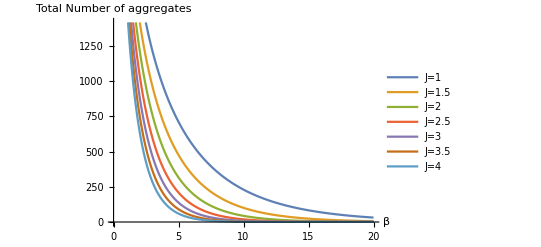

Null

Null

```mathematica
ListLinePlot[{(ⅇ^-J1+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-J1×l))/(ⅇ^-J1+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-J1×l))×10000,(ⅇ^-J105+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-J105×l))/(ⅇ^-J105+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-J105×l))×10000,(ⅇ^-J2+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-J2×l))/(ⅇ^-J2+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-J2×l))×10000,(ⅇ^-J205+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-J205×l))/(ⅇ^-J205+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-J205×l))×10000,(ⅇ^-J3+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-J3×l))/(ⅇ^-J3+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-J3×l))×10000,(ⅇ^-J305+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-J305×l))/(ⅇ^-J305+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-J305×l))×10000,(ⅇ^-J4+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-J4×l))/(ⅇ^-J4+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-J4×l))×10000},DataRange->{0,20},PlotLegends->{"J=1","J=1.5","J=2","J=2.5","J=3","J=3.5","J=4"},AxesLabel->{"β","Total Number of aggregates"}]
```

General::munfl: Exp[-709.379] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-716.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-723.021] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

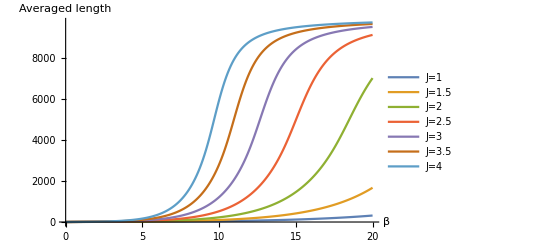

```mathematica
ListLinePlot[{(ⅇ^-J1+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-J1×l))/(ⅇ^-J1+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-J1×l)),(ⅇ^-J105+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-J105×l))/(ⅇ^-J105+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-J105×l)),(ⅇ^-J2+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-J2×l))/(ⅇ^-J2+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-J2×l)),(ⅇ^-J205+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-J205×l))/(ⅇ^-J205+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-J205×l)),(ⅇ^-J3+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-J3×l))/(ⅇ^-J3+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-J3×l)),(ⅇ^-J305+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-J305×l))/(ⅇ^-J305+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-J305×l)),(ⅇ^-J4+gamma×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-J4×l))/(ⅇ^-J4+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-J4×l))},DataRange->{0,20},PlotLegends->{"J=1","J=1.5","J=2","J=2.5","J=3","J=3.5","J=4"},AxesLabel->{"β","Averaged length"}]
```